```mathematica
ClearAll[b]
b[k_]:=Piecewise[{{Cos[k x Pi/2],Mod[k,2]==1},{Sin[k x Pi/2],Mod[k,2]==0}}]
```

```mathematica
b[3]
```

Cos[(3 π x)/2]

```mathematica
vmax=1000.0;
v0=10.0;
a=0.5;
ClearAll[vmax,v0,a]
v=Piecewise[{{vmax,Abs[x]>1},{v0,Abs[x]<a},{0,True}}]
```

Piecewise[{{vmax, Abs[x]>1}, {v0, Abs[x]<a}, {0, True}}]

```mathematica
b[k](-1/2 Laplacian[b[kp],{x}]+v b[kp])
```

(Piecewise[{{Cos[(k π x)/2], Mod[k,2]==1}, {Sin[(k π x)/2], Mod[k,2]==0}, {0, True}}]) ((Piecewise[{{vmax, Abs[x]>1}, {v0, Abs[x]<a}, {0, True}}]) (Piecewise[{{Cos[(kp π x)/2], Mod[kp,2]==1}, {Sin[(kp π x)/2], Mod[kp,2]==0}, {0, True}}])-1/2 (Piecewise[{{-1/4 kp^2 π^2 Cos[(kp π x)/2], Mod[kp,2]==1}, {-1/4 kp^2 π^2 Sin[(kp π x)/2], Mod[kp,2]==0}, {0, True}}]))

```mathematica
Integrate[b[k](-1/2 Laplacian[b[kp],{x}]+v b[kp]),{x,-1,1}]
```

Piecewise[{{-1/((k^2-kp^2) π)4 v0 (-kp Cos[(a kp π)/2] Sin[(a k π)/2]+k Cos[(a k π)/2] Sin[(a kp π)/2]), Mod[k,2]==0&&Mod[kp,2]==0&&0<a<1}, {-1/(2 (k^2-kp^2) π)(kp^2 π^2+8 v0) (-kp Cos[(a kp π)/2] Sin[(a k π)/2]+k Cos[(a k π)/2] Sin[(a kp π)/2]), Mod[k,2]==0&&Mod[kp,2]==0&&a==1}, {1/((k^2-kp^2) π)4 v0 (k Cos[(a kp π)/2] Sin[(a k π)/2]-kp Cos[(a k π)/2] Sin[(a kp π)/2]), Mod[k,2]==1&&Mod[kp,2]==1&&0<a<1}, {1/(2 (k^2-kp^2) π)(kp^2 π^2+8 v0) (k Cos[(a kp π)/2] Sin[(a k π)/2]-kp Cos[(a k π)/2] Sin[(a kp π)/2]), a==1&&Mod[k,2]==1&&Mod[kp,2]==1}, {0, True}}]

```mathematica
b[k]
```

Piecewise[{{Cos[(k π x)/2], Mod[k,2]==1}, {Sin[(k π x)/2], Mod[k,2]==0}, {0, True}}]

```mathematica
r=Out[32];
```

```mathematica
ClearAll[h]
h[k1_,kp1_]:=r/.{k->k1,kp->kp1}
```

```mathematica
h[1,1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 v0 ComplexInfinity)/π encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 (π^2+8 v0) ComplexInfinity)/π encountered.

Piecewise[{{0, a>1||a≤0}, {Indeterminate, True}}]

```mathematica
-1/2Integrate[b[k]Laplacian[b[kp],{x}],{x,-Infinity,Infinity},Assumptions->k∈PositiveIntegers&&kp∈PositiveIntegers]
```

0

```mathematica
b[k]
```

Piecewise[{{Cos[(k π x)/2], Mod[k,2]==1}, {Sin[(k π x)/2], Mod[k,2]==0}, {0, True}}]

```mathematica
Table[b[k],{k,Range[2,6,2]}]
```

{Sin[π x],Sin[2 π x],Sin[3 π x]}

```mathematica
l=Laplacian[b[k],{x}]
```

Piecewise[{{-1/4 k^2 π^2 Cos[(k π x)/2], Mod[k,2]==1}, {-1/4 k^2 π^2 Sin[(k π x)/2], Mod[k,2]==0}, {0, True}}]

```mathematica
FindInstance[Mod[k,2]==1,k,Integers,10]
```

{{k→-823},{k→-733},{k→59},{k→63},{k→275},{k→283},{k→325},{k→537},{k→631},{k→795}}

```mathematica
Table[b[k],{k,Range[1,17,2]}]
```

{Cos[(π x)/2],Cos[(3 π x)/2],Cos[(5 π x)/2],Cos[(7 π x)/2],Cos[(9 π x)/2],Cos[(11 π x)/2],Cos[(13 π x)/2],Cos[(15 π x)/2],Cos[(17 π x)/2]}

```mathematica
D[Cos[((2n+1)Pi x)/2],{x,2}]
```

-1/4 (1+2 n)^2 π^2 Cos[1/2 (1+2 n) π x]

```mathematica
s=Integrate[Cos[((2n+1)Pi x)/2]D[Cos[((2np+1) Pi x)/2],{x,2}],{x,-1,1}]
```

-((π+2 np π)^2 (Sin[(n-np) π]/(n-np)+Sin[(1+n+np) π]/(1+n+np)))/(4 π)

```mathematica
Table[s,{n,0,5},{np,0,5}]//MatrixForm
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

(Indeterminate | 0 | 0 | 0 | 0 | 0
0 | Indeterminate | 0 | 0 | 0 | 0
0 | 0 | Indeterminate | 0 | 0 | 0
0 | 0 | 0 | Indeterminate | 0 | 0
0 | 0 | 0 | 0 | Indeterminate | 0
0 | 0 | 0 | 0 | 0 | Indeterminate)

```mathematica
s//FullSimplify
```

1/8 (1+2 n) π (π+2 n π-Sin[2 n π])

```mathematica
d=Integrate[Sin[((2n)Pi x)/2]D[Sin[((2np)Pi x)/2],{x,2}],{x,-1,1}]
```

(2 np^2 π (np Cos[np π] Sin[n π]-n Cos[n π] Sin[np π]))/(-n^2+np^2)

```mathematica
c=s+d//FullSimplify
```

(2 np^2 π (np Cos[np π] Sin[n π]-n Cos[n π] Sin[np π]))/(-n^2+np^2)-((π+2 np π)^2 (Sin[(n-np) π]/(n-np)+Sin[(1+n+np) π]/(1+n+np)))/(4 π)

```mathematica
Table[-1/2c,{n,0,5},{np,0,5}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 π ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{Indeterminate,0,0,0,0,0},{0,Indeterminate,0,0,0,0},{0,0,Indeterminate,0,0,0},{0,0,0,Indeterminate,0,0},{0,0,0,0,Indeterminate,0},{0,0,0,0,0,Indeterminate}}

```mathematica
Table[s*d,{n,0,5},{np,0,5}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{Indeterminate,0,0,0,0,0},{0,Indeterminate,0,0,0,0},{0,0,Indeterminate,0,0,0},{0,0,0,Indeterminate,0,0},{0,0,0,0,Indeterminate,0},{0,0,0,0,0,Indeterminate}}

```mathematica
Table[(Pi^2 k^2)/8,{k,0,5}]
```

{0,π^2/8,π^2/2,(9 π^2)/8,2 π^2,(25 π^2)/8}

```mathematica
v0 Integrate[Cos[],{x,-a,a}]
```

```mathematica
Cos[((2n+1)Pi x)/2]D[Cos[((2np+1) Pi x)/2],{x,2}]
```

-1/4 (1+2 np)^2 π^2 Cos[1/2 (1+2 n) π x] Cos[1/2 (1+2 np) π x]

```mathematica
Integrate[Cos[1/2 (1+2 n) π x] Cos[1/2 (1+2 np) π x],{x,-a,a}]
```

(Sin[a (n-np) π]/(n-np)+Sin[a (1+n+np) π]/(1+n+np))/π

```mathematica
z=Out[137];
```

```mathematica
a=1/2;
z
```

(Sin[1/2 (n-np) π]/(n-np)+Sin[1/2 (1+n+np) π]/(1+n+np))/π

```mathematica
Table[z,{n,0,5},{np,0,5}]//MatrixForm
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

(Indeterminate | 1/π | -1/(3 π) | -1/(3 π) | 1/(5 π) | 1/(5 π)
1/π | Indeterminate | 1/π | 1/(5 π) | -1/(3 π) | -1/(7 π)
-1/(3 π) | 1/π | Indeterminate | 1/π | -1/(7 π) | -1/(3 π)
-1/(3 π) | 1/(5 π) | 1/π | Indeterminate | 1/π | 1/(9 π)
1/(5 π) | -1/(3 π) | -1/(7 π) | 1/π | Indeterminate | 1/π
1/(5 π) | -1/(7 π) | -1/(3 π) | 1/(9 π) | 1/π | Indeterminate)

```mathematica
10Integrate[Sin[Pi x]^2,{x,-a,a}]
```

5

```mathematica
(g=Table[-1/2 Integrate[b[k]D[b[kp],{x,2}],{x,-1,1}],{k,1,6},{kp,1,6}])//MatrixForm
```

(π^2/8 | 0 | 0 | 0 | 0 | 0
0 | π^2/2 | 0 | 0 | 0 | 0
0 | 0 | (9 π^2)/8 | 0 | 0 | 0
0 | 0 | 0 | 2 π^2 | 0 | 0
0 | 0 | 0 | 0 | (25 π^2)/8 | 0
0 | 0 | 0 | 0 | 0 | (9 π^2)/2)

```mathematica
ClearAll[n]
Diagonal[g]//FindSequenceFunction[#,n]&
```

(n^2 π^2)/8

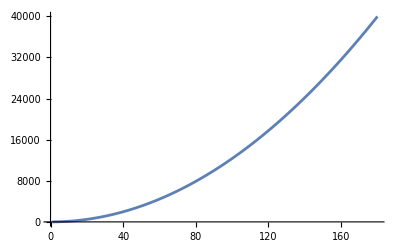

```mathematica
ListLinePlot@g
```

```mathematica
ClearAll[a]
fit=NonlinearModelFit[g,a x^2+b,{a,b},x]
```

FittedModel[…]

```mathematica
n=fit["BestFitParameters"][[1]][[2]]
```

1.2337

```mathematica
Rationalize[n,0.001]
```

37/30

```mathematica
n+1
```

2.2337

```mathematica
Pi^2/8//N
```

1.2337

```mathematica
(g=Table[-1/2 Integrate[b[k]D[b[kp],{x,2}],{x,-1,1}],{k,1,6},{kp,1,6}])//MatrixForm
```

(π^2/8 | 0 | 0 | 0 | 0 | 0
0 | π^2/2 | 0 | 0 | 0 | 0
0 | 0 | (9 π^2)/8 | 0 | 0 | 0
0 | 0 | 0 | 2 π^2 | 0 | 0
0 | 0 | 0 | 0 | (25 π^2)/8 | 0
0 | 0 | 0 | 0 | 0 | (9 π^2)/2)

```mathematica
ClearAll[c]
a=1/2;
(c=Table[ Subscript[V, 0] Integrate[b[k]b[kp],{x,-a,a}],{k,1,6},{kp,1,6}])//MatrixForm
```

(10 (1/2+1/π) | 0 | 10/π | 0 | -10/(3 π) | 0
0 | 5 | 0 | 40/(3 π) | 0 | 0
10/π | 0 | 10 (1/2-1/(3 π)) | 0 | 10/π | 0
0 | 40/(3 π) | 0 | 5 | 0 | 8/π
-10/(3 π) | 0 | 10/π | 0 | 10 (1/2+1/(5 π)) | 0
0 | 0 | 0 | 8/π | 0 | 5)

```mathematica
ClearAll[V]
Eigensystem[g+c]
```

{{(Root3.75 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,3]3745.636803501217)/(24 π),(Root2.79 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,3]2786.323238599703)/(24 π),(Root1.93 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,2]1931.3588547340892)/(24 π),(Root1.22 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,2]1220.4508452698794)/(24 π),(Root663.Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,1]663.0321793473894)/(24 π),(Root588.Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,1]587.8583228542243)/(24 π)},{{0,-3/5+1/192 (120 π+108 π^3-Root3.75 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,3]3745.636803501217) ((3 π)/8+(3 π^3)/20-1/320 Root3.75 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,3]3745.636803501217),0,1/192 (-120 π-108 π^3+Root3.75 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,3]3745.636803501217),0,1},{1/80 (48+120 π+75 π^3-Root2.79 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,3]2786.323238599703)-(9 (128+120 π+75 π^3-Root2.79 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,3]2786.323238599703))/(640+120 π+27 π^3-Root2.79 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,3]2786.323238599703),0,-(3 (128+120 π+75 π^3-Root2.79 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,3]2786.323238599703))/(640+120 π+27 π^3-Root2.79 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,3]2786.323238599703),0,1,0},{0,-3/5+1/192 (120 π+108 π^3-Root1.93 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,2]1931.3588547340892) ((3 π)/8+(3 π^3)/20-1/320 Root1.93 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,2]1931.3588547340892),0,1/192 (-120 π-108 π^3+Root1.93 × 10^3Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,2]1931.3588547340892),0,1},{1/80 (48+120 π+75 π^3-Root1.22 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,2]1220.4508452698794)-(9 (128+120 π+75 π^3-Root1.22 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,2]1220.4508452698794))/(640+120 π+27 π^3-Root1.22 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,2]1220.4508452698794),0,-(3 (128+120 π+75 π^3-Root1.22 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,2]1220.4508452698794))/(640+120 π+27 π^3-Root1.22 × 10^3Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,2]1220.4508452698794),0,1,0},{0,-3/5+1/192 (120 π+108 π^3-Root663.Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,1]663.0321793473894) ((3 π)/8+(3 π^3)/20-1/320 Root663.Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,1]663.0321793473894),0,1/192 (-120 π-108 π^3+Root663.Root[16711680 π+9773568 π^3-2419200 π^5-846720 π^7-62208 π^9+(-139264+43200 π^2+40320 π^4+7056 π^6) #1+(-360 π-168 π^3) #1^2+#1^3&,1]663.0321793473894),0,1},{1/80 (48+120 π+75 π^3-Root588.Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,1]587.8583228542243)-(9 (128+120 π+75 π^3-Root588.Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,1]587.8583228542243))/(640+120 π+27 π^3-Root588.Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,1]587.8583228542243),0,-(3 (128+120 π+75 π^3-Root588.Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,1]587.8583228542243))/(640+120 π+27 π^3-Root588.Root[26214400+15974400 π-2995200 π^2+4078080 π^3-2361600 π^4-1512000 π^5-471888 π^6-279720 π^7-6075 π^9+(-133120+49920 π+43200 π^2+19680 π^3+25200 π^4+2331 π^6) #1+(-208-360 π-105 π^3) #1^2+#1^3&,1]587.8583228542243),0,1,0}}}